## IntertiaMatrix-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 18:26:11
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

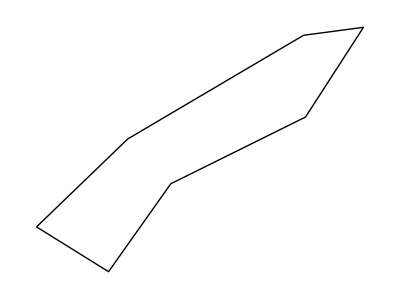

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
Boundary[polygon]
```

```mathematica
InertiaMatrix[polygon]
```

{{0.110189,0.0605324},{0.0605324,0.0490591}}

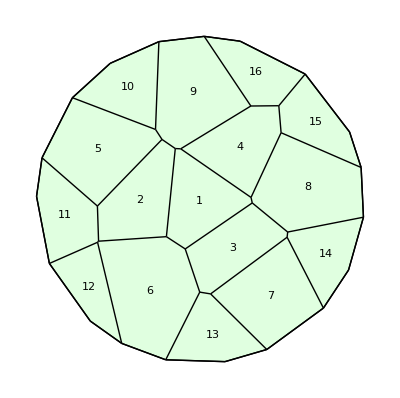

```mathematica
w=TemplateRandomCircularGrid[16,100];
ShowTissue[w, "CellNumbers"-> True]
```

```mathematica
MatrixForm[InertiaMatrix[w,3]]
```

(1.06784×10^6 | 845513.
845513. | 1.74888×10^6)

```mathematica
MatrixForm/@InertiaMatrix[w]
```

{(259891. | 6981.2
6981.2 | 322737.),(2.86007×10^6 | 158179.
158179. | 442006.),(1.06784×10^6 | 845513.
845513. | 1.74888×10^6),(1.41873×10^6 | 1.53925×10^6
1.53925×10^6 | 2.26219×10^6),(1.09442×10^7 | 5.12843×10^6
5.12843×10^6 | 3.08077×10^6),(3.81264×10^6 | 5.51735×10^6
5.51735×10^6 | 1.11918×10^7),(4.95471×10^6 | 6.03269×10^6
6.03269×10^6 | 8.73977×10^6),(1.2946×10^7 | 1.38586×10^6
1.38586×10^6 | 698470.),(536568. | 778358.
778358. | 1.24194×10^7),(3.2941×10^6 | 4.69222×10^6
4.69222×10^6 | 7.49578×10^6),(1.05182×10^7 | 1.09109×10^6
1.09109×10^6 | 431390.),(5.48916×10^6 | 4.13327×10^6
4.13327×10^6 | 3.53616×10^6),(319327. | 896276.
896276. | 1.00221×10^7),(8.12383×10^6 | 3.41917×10^6
3.41917×10^6 | 1.68668×10^6),(6.84929×10^6 | 4.36847×10^6
4.36847×10^6 | 3.21066×10^6),(1.73251×10^6 | 3.36417×10^6
3.36417×10^6 | 8.09889×10^6)}